```mathematica
(* Primeira Equação: -9y δϕ/δx+4x δϕ/δy*)
```

```mathematica
(* Condição Inicial: ϕ[t]==Sin[t^2] *)
```

```mathematica
v[x_,y_]:={-9y,4x}
```

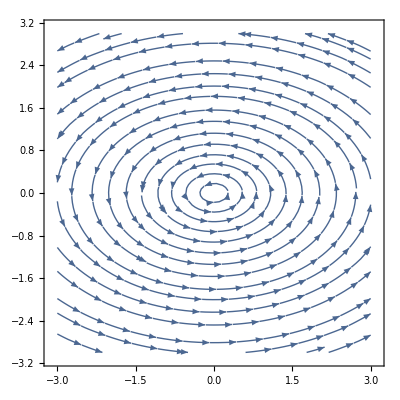

```mathematica
campo=StreamPlot[v[x,y],{x,-3,3},{y,-3,3},StreamStyle->{Thin}]
```

```mathematica
(* Obtenção dos contornos *)
```

```mathematica
solsDif=DSolve[y'[x]==(-4x)/(9y[x]),y[x],x]
```

{{y[x]→-1/3 √2 √(-2 x^2+9 C[1])},{y[x]→1/3 √2 √(-2 x^2+9 C[1])}}

```mathematica
r1=Solve[y==solsDif[[1]][[1]][[2]],C[1]]
```

{{C[1]→1/18 (4 x^2+9 y^2)}}

```mathematica
g[x_,y_]:=r1[[1,1,2]]
```

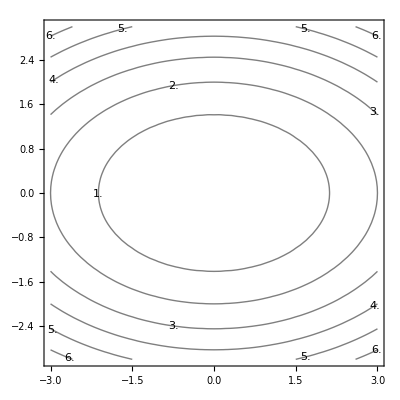

```mathematica
contornos=ContourPlot[g[x,y],{x,-3,3},{y,-3,3},ContourShading->False,ContourLabels->True,ContourStyle->{Thin}]
```

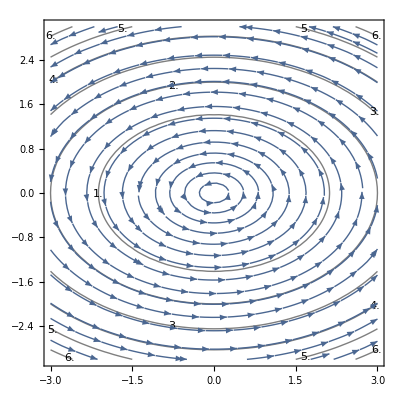

```mathematica
Show[contornos,campo]
```

```mathematica
Plot3D[Sin[(4 x^2+9 y^2)/13],{x,-2,2},{y,-2,2},PlotPoints->80,PlotStyle->{Opacity[.3],Blue},MeshFunctions->{#3&},BoundaryStyle->Directive[Red, Thick]]
```

-Graphics3D-